```mathematica
SetDirectory[NotebookDirectory[]];
```

# Produce data

```mathematica
sigma0=Import["../../sigma0.dat"];
sigma0p2=Import["../../sigma0p2.dat"];
```

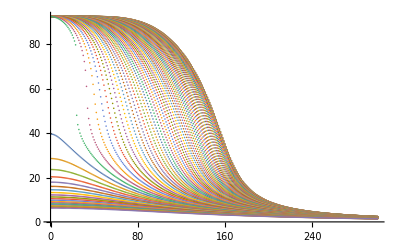

```mathematica
ListPlot[sigma0,PlotRange->All]
```

```mathematica
mu=Table[i*5.,{i,1,80}];
mu2=Table[i,{i,290,310}];
T=Table[i,{i,1,300}];
hin=Flatten[Import["./mub0/buffer/h.dat"]];
Zphiin=Flatten[Import["./mub0/buffer/Zphi.dat"]];
Zpsiin=Flatten[Import["./mub0/buffer/Zpsi.dat"]];
hqcd=hin(**√Zphiin*Zpsiin*);
hqcdin=hqcd/hqcd[[1]]*6.5;
```

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,hqcdin[[i]],N[i],mu[[j]],300.],{i,1,250}],{j,1,80}];
```

```mathematica
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,hqcdin[[i]],N[i],mu2[[j]],300.],{i,1,250}],{j,1,21}];
```

```mathematica
(*Export["./Zdata.dat",Zdata];
Export["./Zdatap2.dat",Zdatap2];*)
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,250},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,250},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,250},{j,62,80}],1];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["M=300 MeV with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->Pink,PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Red,PointSize[Medium]}(*,PlotLegends->{"CEP"}*)]],ImageResolution->300]
```

-Graphics-

```mathematica
Export["phaseQCDinput.pdf",phaseplot];
```